```mathematica
Clear[xϕ,yϕ,zϕ];
t[0,0,0]
```

{{0.390034,-0.379638,0.515992,1.13621},{-0.0427227,0.587348,0.464432,-0.294683},{-0.639178,-0.270919,0.283822,4.62436},{0.,0.,0.,1.}}

```mathematica
Clear[t,VM];
Prepend0[s_]:=If[StringLength[s]≤1,"0"<>s,s]
To0String[n_]:=Prepend0[ToString[n]]
Clear[xϕ,yϕ,zϕ];
width=1;
VP={-1.368735891197894,2.4239630408225583,-1.923789291183669};
VV={0.8041248305969765,-0.26246420928114034,1.0667629458578127};
p={{2.2238114193406564,0.,0.5,0.},{0.,2.2238114193406564,0.5,0.},{0.,0.,4.8239698107859965,-15.621823696072125},{0.,0.,1.,0.}}(*{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}*);
t[xϕ_,yϕ_,zϕ_]:=Evaluate[Simplify[{{-0.19137044250334137,0.20577883813192122,0.4135606648523913,2.1958945431894474*^-16},{0.41926530011485547,0.26527480855822433,0.06201519220318221,3.2928378766974304*^-17},{0.1938916239956629,-0.3705190220777795,0.27408336765088553,3.383784863137726},{0.,0.,0.,1.}}.{{-0.865937428730059,1.0655095412692892,0.6040213464675591,-0.4017967295033945},{1.22302008404747,0.7122703967935252,0.49688304043115944,-1.216086760636077},{-0.06613806423605778,-0.7793332402225015,1.2799474431176479,3.1665467938081817},{0.,0.,0.,1.}}.Inverse[TransformationMatrix[RescalingTransform[{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}].RotationTransform[0,{0,1,0}].RotationTransform[0,{1,0,0}].RotationTransform[0,{0,0,1}]]].TransformationMatrix[
RescalingTransform[{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}].RotationTransform[yϕ,{0,1,0}].RotationTransform[xϕ,{1,0,0}].RotationTransform[zϕ,{0,0,1}]]]];
(*VM[xϕ_,yϕ_,zϕ_]:={t[xϕ,yϕ,zϕ],p};*)
VM={{{-0.19517340732559396,0.20352751372167174,0.4128969511042586,2.1881158665059822*^-16},{0.4213747037084222,0.25955388926026446,0.07124000031239328,3.77530942276389*^-17},{0.18533941876340612,-0.3757769680650281,0.2728387254850339,3.383784863137727},{0.,0.,0.,1.}},{{2.2324753640197192,0.,0.5,0.},{0.,2.2324753640197197,0.5,0.},{0.,0.,4.8510558279186,-15.717393531176063},{0.,0.,1.,0.}}};
MkMost[minϕ_,maxϕ_,sgn_,offset_]:=MkMost[minϕ,maxϕ,sgn,offset]=
{
ParametricPlot3D[{ρ Cos[ϕ],ρ Sin[ϕ],z}/.ρ->1,{ϕ,minϕ,maxϕ},{z,-width/2,-(width/2-0.02)},PlotRange->{{-1,1},{-1,1},{-width/2,width/2}},PlotStyle->Black,Boxed->False,Axes->None,Mesh->None],
ParametricPlot3D[{ρ Cos[ϕ],ρ Sin[ϕ],z}/.ρ->1,{ϕ,minϕ,maxϕ},{z,width/2-0.02,width/2},PlotRange->{{-1,1},{-1,1},{-width/2,width/2}},PlotStyle->Black,Boxed->False,Axes->None,Mesh->None],
Graphics3D[{Gray,EdgeForm->None,Cylinder[Table[{{ρ Cos[ϕ],ρ Sin[ϕ],-width/2},{ρ Cos[ϕ],ρ Sin[ϕ],width/2}}/.ρ->1,{ϕ,minϕ,maxϕ-(maxϕ-minϕ)/10,(maxϕ-minϕ)/10}],0.01]}],
ParametricPlot3D[Evaluate[RotationMatrix[offset,{0,0,1}].{x,y,sgn width/2}],{x,-1,1},{y,-0.05,.05},PlotStyle->Black,Boxed->False,Axes->None,Mesh->None]}(*,
ViewPoint->VP,ViewVertical->VV,ImageSize->Large*);
DoShowF[xϕ_,yϕ_,zϕ_,offset_]:=Show[MkMost[-2π/20+2 2π/20+Mod[offset,2π/20],-2π/20+π+2 2π/20+Mod[offset,2π/20],-1,offset],ViewPoint->VP,ViewVertical->VV,ImageSize->{700,Automatic},ViewMatrix->VM(*[xϕ,yϕ,zϕ]*)]
DoShowB[xϕ_,yϕ_,zϕ_,offset_]:=Show[MkMost[-2π/20+π+2 2π/20+Mod[offset,2π/20],-2π/20+2π+2 2π/20+Mod[offset,2π/20],1,offset],ViewPoint->VP,ViewVertical->VV,ImageSize->{700,Automatic},ViewMatrix->VM(*[xϕ,yϕ,zϕ]*)]
(*Manipulate[DoShowF[xϕ,yϕ,zϕ,offset],{xϕ,0,2π},{yϕ,0,2π},{zϕ,0,2π},{offset,0,2π,2π/20/5}]
Manipulate[DoShowB[xϕ,yϕ,zϕ,offset],{xϕ,0,2π},{yϕ,0,2π},{zϕ,0,2π},{offset,0,2π,2π/20/5}]*)
min=0;max=2π;step=2π/20/5;
Fronts=Table[DoShowF[0,0,0,min+i*step],{i,0,(max-min)/step}];
Backs=Table[DoShowB[0,0,0,min+i*step],{i,0,(max-min)/step}];
(*Flatten[Table[{
{FileNameJoin[{NotebookDirectory[],"Hamster_"<>To0String[i]<>"_of_"<>To0String[(max-min)/step]<>"_Front.png"}],DoShowF[0,0,0,min+i*step]},
{FileNameJoin[{NotebookDirectory[],"Hamster_"<>To0String[i]<>"_of_"<>To0String[(max-min)/step]<>"_Back.png"}],DoShowB[0,0,0,min+i*step]}
},{i,0,(max-min)/step}],1]*)
(*Map[Export[#⟦1⟧,#⟦2⟧,Background->None]&,%]*)
(*Export[FileNameJoin[{NotebookDirectory[],"Hamster_01_Front.png"}],%,Background->None]
Show[MkMost[π+2 2π/20,2π+2 2π/20,1],ViewPoint->VP,ViewVertical->VV,ImageSize->Large,ViewMatrix->VM]
Export[FileNameJoin[{NotebookDirectory[],"Hamster_01_Behind.png"}],%,Background->None]
Show[Map[Rotate[#1,2π/40,{0,0,1}]&,MkMost[2 2π/20,π+2 2π/20,-1]],ViewPoint->VP,ViewVertical->VV,ImageSize->Large,ViewMatrix->VM]*)
```

```mathematica
ClearAll[unground0];
unground0[img_]:=unground0[img]=With[{mask=ChanVeseBinarize[img,TargetColor->{1.,1.,1.}]},Rasterize[SetAlphaChannel[img,ImageApply[1-#&,mask]],Background->None]]
```

```mathematica
ClearAll[AllRoosters,MemoImageCompose];
Roosters0=Map[Show[#,ImageSize->{5}]&,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}];
AllRoosters=Flatten[Table[Roosters0,{20}]];
MemoImageCompose[l___]:=MemoImageCompose[l]=ImageCompose[l]
```

```mathematica
ImageCompose[Backs⟦1⟧,Fronts⟦1⟧]
```

-Graphics-

```mathematica
Graphics[{Inset[-Graphics-]}]
```

-Graphics-

```mathematica
pre=Show[DoShowB[0,0,0,0],DoShowF[0,0,0,0]];
```

```mathematica
Manipulate[ImageCrop[Show[pre,Graphics3D[{Inset[-Graphics-,{x,y,z},Automatic,ImageScaled[sz]]}]]],{{x,-0.445},-1,1},{{y,-0.055},-1,1},{{z,0},-1,1},{{sz,0.4},0,1}]
```

```mathematica
ClearAll[MakeN,MakeRooster,MakeInset];
MakeInset[img_]:=MakeInset[img]=Inset[Show[img,ImageSize->Large],{-.445,-.055,0},Automatic,ImageScaled[0.4/Max[Map[#⟦2⟧&,Map[ImageDimensions,Roosters0]]] ImageDimensions[img]]]
MakeRooster[n_]:=MakeRooster[n]=Graphics3D[{MakeInset[AllRoosters⟦Mod[n-1,5]+1⟧]}]
MakeN[n_]:=ImageCrop[Show[Backs⟦n⟧,Fronts⟦n⟧,MakeRooster[n]]]
```

```mathematica
Roosters1=Map[Show[#,ImageSize->Small]&,Roosters0]
```

```mathematica
n=50;
foo=Table[MakeN[k],{k,1,n}];
Animate[foo⟦k⟧,{k,1,n,1},AnimationRate->0.1,AnimationRunning->False]
Export[FileNameJoin[{NotebookDirectory[],"rooster_hamster_wheel.gif"}],foo,AnimationRepetitions->∞,Background->None,DisplayDurations->0.1]
```

D:\Documents\SkyDrive\MIT\2014 Summer\ITP\rooster_hamster_wheel.gif

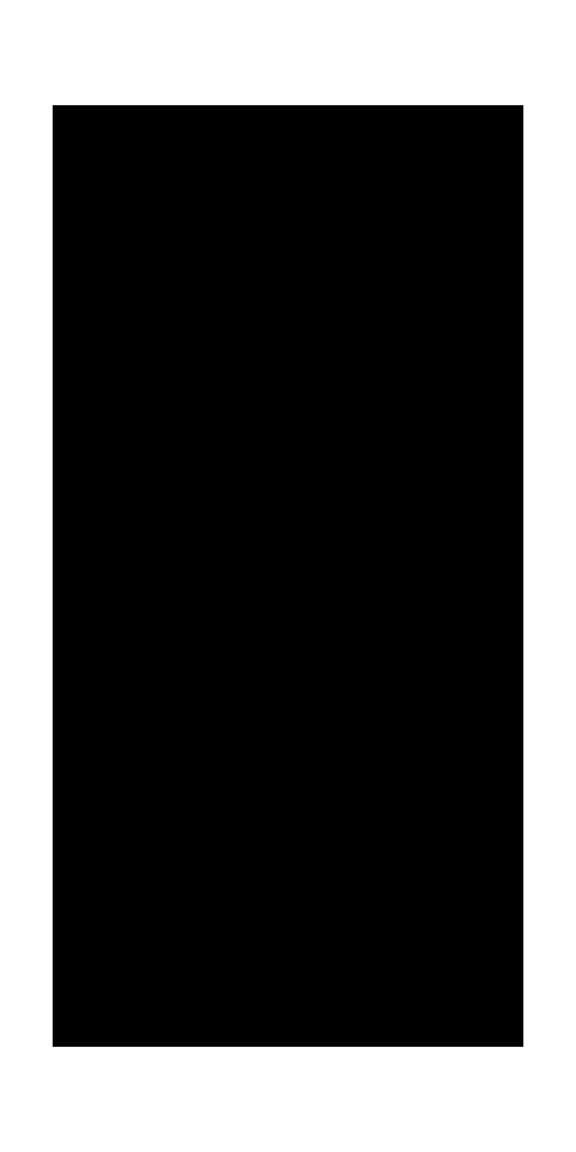

```mathematica
Show[Graphics[Rectangle[{-1,-1},{0,1}]],ImageSize->Large]
```

```mathematica
ImageAspectRatio[Graphics[r1]]
```

359/360

```mathematica
r1=Rectangle[{-1,-1},{1,1}];
r2=Rectangle[{-1,-1},{0,1}];
f[img_]:=Show[ParametricPlot3D[{{t,0,0},{0,t,0},{0,0,t}},{t,-1,1}],Graphics3D[{Inset[Show[Graphics[img],ImageSize->Large],{0.25,0,0},Automatic,ImageScaled[{0.25/ImageAspectRatio[Graphics[img]],0.25}]]}]]
f[r1]
f[r2]
```

-Graphics3D-

-Graphics3D-

```mathematica
Graphics3D[{Inset[Show[Graphics[Rectangle[{-1,-1},{1,1}]],ImageSize->Large,AspectRatio->1],{-.445,-.055,0},Automatic,ImageScaled[0.4]]}]
```

-Graphics3D-